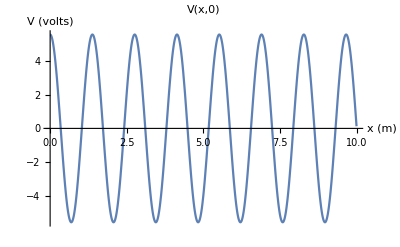

```mathematica
v0R = 5;
v0L = 5/9;
w = 2 Pi (150 *10^6);
c = 3 * 10^8;
k= w/ (0.69 c);

v[x_, t_] := v0R Cos[k x - w t ] + v0L Cos[k x - w t];

Plot[v[x,0],{x,0,10},PlotLabel->"V(x,0)",AxesLabel->{"x (m)","V (volts)"}]
```

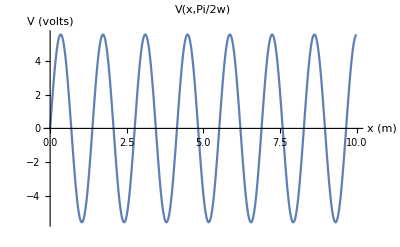

```mathematica
Plot[v[x,Pi / (2 w)],{x,0,10},PlotLabel->"V(x,Pi/2w)",AxesLabel->{"x (m)","V (volts)"}]
```

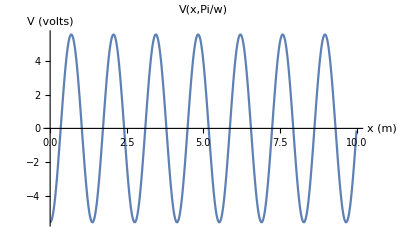

```mathematica
Plot[v[x,Pi / (w)],{x,0,10},PlotLabel->"V(x,Pi/w)",AxesLabel->{"x (m)","V (volts)"}]
```

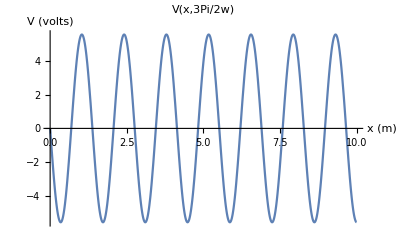

```mathematica
Plot[v[x,3 Pi / (2 w)],{x,0,10},PlotLabel->"V(x,3Pi/2w)",AxesLabel->{"x (m)","V (volts)"}]
```